```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes"]
```

C:\Users\pglpm\repositories\genobayes

```mathematica
NS["study_dirichlet_type_iii_4"]
```

```mathematica
assu=(aa>0&&ax>0&&nx>0&&t>0&&f1>0&&f2>0&&f3>0)
```

aa>0&&ax>0&&nx>0&&t>0&&f1>0&&f2>0&&f3>0

```mathematica
ClearAll[dirich];dirich[aa_,nx_,f_,t_]:=FS[(Multinomial@@(nx*f))*Gamma[aa]/Gamma[nx+aa]*(Times@@Gamma[nx*f+aa/t])/Gamma[aa/t]^t]
```

```mathematica
Assuming[assu,FS@D[dirich[aa,nx,{f1,f2,f3},t],aa]]
```

1/(t Gamma[aa+nx])Gamma[aa] Gamma[f1 nx+aa/t] Gamma[f2 nx+aa/t] Gamma[f3 nx+aa/t] Gamma[aa/t]^-t Multinomial[f1 nx,f2 nx,f3 nx] (t PolyGamma[0,aa]+PolyGamma[0,f1 nx+aa/t]+PolyGamma[0,f2 nx+aa/t]+PolyGamma[0,f3 nx+aa/t]-t (PolyGamma[0,aa+nx]+PolyGamma[0,aa/t]))

```mathematica
nn=5*10^6;
```

```mathematica
data=Import["scripts\\dataset1_simple.csv"];
n=Length[data[[;;,1]]];
Dimensions[data]
```

{6029,97}

```mathematica
labels[ng_]:=
SortBy[Tally[data[[;;,Join[{1,2,3},ng]]]],FromDigits[#[[1]],2]&][[;;,1]];ClearAll[fs];fs[ng_]:=fs[ng]=
SortBy[Tally[data[[;;,Join[{1,2,3},ng]]]],FromDigits[#[[1]],2]&][[;;,2]]/n
```

```mathematica
derd[aa_,nx_,t_]=Assuming[assu,FS[D[Log[sdir[aa,nx,t]],aa]]]
```

PolyGamma[0,aa]-PolyGamma[0,aa+nx]-PolyGamma[0,aa/t]+PolyGamma[0,(aa+nx)/t]

```mathematica
Assuming[assu,FS@Limit[derd[aa,nx,t],t->+Infinity]]
```

∞

```mathematica
Assuming[assu,FS@Series[derd[aa,nx,t],{t,+Infinity,4}]]
```

(nx t)/(aa (aa+nx))+(PolyGamma[0,aa]-PolyGamma[0,aa+nx])+(nx π^2)/(6 t)-(nx (2 aa+nx) Zeta[3])/t^2+(nx (3 aa^2+3 aa nx+nx^2) π^4)/(90 t^3)-(nx (2 aa+nx) (2 aa^2+2 aa nx+nx^2) Zeta[5])/t^4+O[1/t]^5

```mathematica
FindRoot[(nx t)/(aa (aa+nx))+(PolyGamma[0,aa]-PolyGamma[0,aa+nx])==0,aa]
```

Solve[(nx t)/(aa (aa+nx))+PolyGamma[0,aa]-PolyGamma[0,aa+nx]==0,aa]

```mathematica
ClearAll[ddir];ddir[nx_,f_,t_]:=ddir[nx,f,t]=Function[aa,
(*(Multinomial@@(nx*f))**)Gamma[aa]/Gamma[nx+aa]*(Times@@Gamma[nx*f+aa/t])/Gamma[aa/t]^Length[f]]
```

```mathematica
ddir[n,fs[{1}],4][100]//N
```

9.73068431445247×10^-4427

```mathematica
ClearAll[lddir];lddir[nx_,f_,t_]:=lddir[nx,f,t]=Function[aa,
(*(Multinomial@@(nx*f))**)LogGamma[aa]-LogGamma[nx+aa]+(Total@LogGamma[nx*f+aa/t])-Length[f]*LogGamma[aa/t]]
```

```mathematica
lsdir[aa_,nx_,t_]=LogGamma[aa]-LogGamma[aa+nx]+t*(LogGamma[(aa+nx)/t]-LogGamma[aa/t])
```

LogGamma[aa]-LogGamma[aa+nx]+t (-LogGamma[aa/t]+LogGamma[(aa+nx)/t])

```mathematica
ClearAll[con];con[f_]:=con[f]=1/NIntegrate[ddir[ax,n,f],{ax,0,10^6}]
```

```mathematica
ClearAll[nddir];nddir[aa_,nx_,f_]:=ddir[aa,nx,f]*con[f]
```

```mathematica
list0=FoldList[Join,{6},T@{{57,32,66,75,88,93,22,14,21,43,89,70,90}}]
```

{{6},{6,57},{6,57,32},{6,57,32,66},{6,57,32,66,75},{6,57,32,66,75,88},{6,57,32,66,75,88,93},{6,57,32,66,75,88,93,22},{6,57,32,66,75,88,93,22,14},{6,57,32,66,75,88,93,22,14,21},{6,57,32,66,75,88,93,22,14,21,43},{6,57,32,66,75,88,93,22,14,21,43,89},{6,57,32,66,75,88,93,22,14,21,43,89,70},{6,57,32,66,75,88,93,22,14,21,43,89,70,90}}

```mathematica
listsample:=Block[{rsam=RandomSample[Range[94],Length@Last[list0]]},FoldList[Join,{rsam[[1]]},T@{rsam[[2;;]]}]]
```

```mathematica
listsample0=listsample;
```

```mathematica
ClearAll[maxi];maxi[k_]:=maxi[k]={#[[1]],ax/.#[[2]]}&@NMaximize[{lddir[n,fs[k],2^(Length[k]+3)][ax]-Log[ax],1<ax<10^9},ax];
```

```mathematica
maxi[listsample0[[2]]]
```

{-14470.8,3.15289}

```mathematica
ClearAll[smaxi];smaxi[t_]:=smaxi[t]={#[[1]],ax/.#[[2]]}&@NMaximize[{lsdir[ax,n,2^(t+3)]-Log[ax],1<ax<10^9},ax];
```

```mathematica
smaxi[2]
```

{-20907.3,87431.9}

```mathematica
lddir[n,fs[listsample0[[2]]],2^(2+3)][3.15]
```

-14469.6

```mathematica
lsdir[87431
```

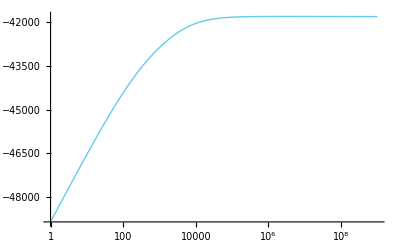

```mathematica
LogLinearPlot[lsdir[ax,n,2^10]-Log@ax,{ax,1,10^9}]
```

```mathematica
gtabcomp=Table[
maxt=maxi[k];
maxp=Exp@maxt[[1]];maxa=(ax/.maxt[[2]]);
std=10/Sqrt@Abs@lddir2[maxa,n,fs[k]];
gauf[ax_]=gaun[n,fs[k],maxa][ax];
Plot[{ddir[ax,n,fs[k]]/ax/maxp,gauf[ax]},{ax,Max[maxa-std,0],maxa+std},PlotRange->{0,1},Frame->Auto,Axes->None,FrameStyle->Directive[Black,Bold,18],
PlotLegends->Auto,FrameLabel->{{p[A | Length[k]],None},{A,None}}],{k,list0[[1;;11]]}];
```

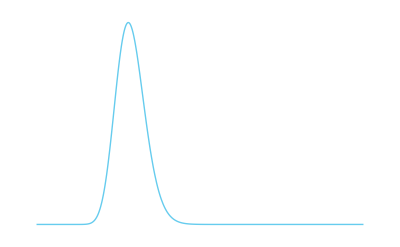

```mathematica
tgenes=listsample[[3]];
fr=fs[tgenes];
tx=2^(Length@tgenes+3);
sample=Sort@RandomSample[Range[Length@fr],Min[16,Length@fr]];
maxp=Exp[maxi[tgenes][[1]]];maxa=maxi[tgenes][[2]];fun[ax_]=Simplify[ddir[n,fr,tx][ax]/ax/maxp];

Plot[fun[ax],{ax,Max[maxa-100,0],maxa+100},PlotRange->{0,1},Frame->Auto,Axes->None,FrameStyle->Directive[Black,Bold,18],
PlotLegends->Auto,FrameLabel->{{p[A | Length[k]],None},{A,None}}]
```

```mathematica
tgenes=listsample[[1]];
fr=fs[tgenes];
tx=2^(Length@tgenes+3);
sample=Sort@RandomSample[Range[Length@fr],Min[16,Length@fr]];
maxp=Exp[maxi[tgenes][[1]]];maxa=maxi[tgenes][[2]];fun[ax_]=Simplify[ddir[n,fr,tx][ax]/ax/maxp];
```

```mathematica
gtabcomp//MF
```

```mathematica
Length[fr]
```

387

```mathematica
2^(6)
```

64

```mathematica
64*8
```

512

```mathematica
tgenes
```

{32,89,88,91,18,53}

```mathematica
tgenes=listsample[[4]];
fr=fs[tgenes];
tx=2^(Length@tgenes+3);
sample=Sort@RandomSample[Range[Length@fr],Min[16,Length@fr]];
maxp=Exp[maxi[tgenes][[1]]];maxa=maxi[tgenes][[2]];fun[ax_]=Simplify[ddir[n,fr,tx][ax]/ax/maxp];
inta=NIntegrate[aa/(n+aa)*fun[aa],{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2];
int1=NIntegrate[fun[aa],{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2];
af=fr-(fr-1/tx)*inta/int1;
```

```mathematica
mf=(n*fr+maxa/tx)/(n+maxa);
```

```mathematica
cf=(n*fr+tx/tx)/(n+tx);
```

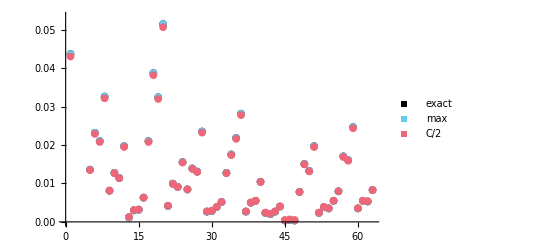

```mathematica
ListPlot[{af,mf,cf},PlotStyle->{Black,blue,red},PlotStyle->Opacity[0.5],PlotLegends->Placed[PointLegend[{Black,blue,red},{"exact","max","C/2"},LegendMarkerSize->Auto,LegendMarkers->Style[■,40]],Bottom]]
```

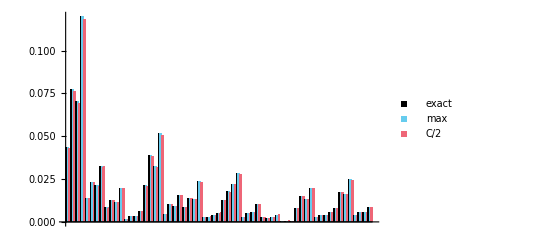

```mathematica
BarChart[T@{af,mf,cf},ChartLayout->"Grouped",ChartStyle->{Black,blue,red},ChartLegends->Placed[PointLegend[{Black,blue,red},{"exact","max","C/2"},LegendMarkerSize->Auto,LegendMarkers->Style[■,40]],Bottom]]
```

```mathematica
expdf["comparefinalfreqs_1",%]
```

comparefinalfreqs_1.pdf

```mathematica
{Max[Abs[mf-af]/af],Max[Abs[cf-af]/af]}*100
```

{0.147003,38.3309}

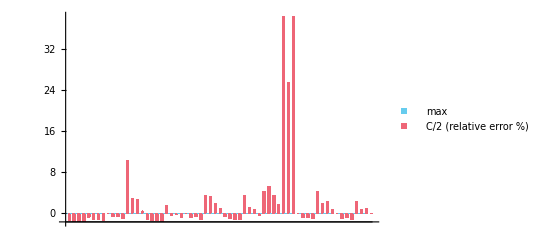

```mathematica
BarChart[T@{mf-af,cf-af}/af*100,ChartLayout->"Grouped",ChartStyle->{blue,red},ChartLegends->Placed[PointLegend[{blue,red},{"max","C/2    (relative error %)"},LegendMarkerSize->Auto,LegendMarkers->Style[■,40]],Bottom]]
```

```mathematica
expdf["comparefinalfreqs_diff_1",%]
```

comparefinalfreqs_diff_1.pdf

```mathematica
(* Compare with gene 9 *)
```

```mathematica
fr=fs[{9}];tx=Length[fr];
maxa=(ax/.maxi[{9}][[2]]);fun[ax_]=FS[ddir[ax,n,fr]/maxa];
af9=NIntegrate[(n*fr+aa/tx)/(n+aa)*fun[aa],{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2];
af9=af9/Total[af9]
```

{0.135916,0.265662,0.0228634,0.0430277,0.0628615,0.119718,0.0240204,0.049639,0.0331108,0.0709603,0.00418693,0.00831928,0.0236898,0.0474903,0.0228634,0.0656713}

```mathematica
mf9=(n*fr+maxa/tx)/(n+maxa)
```

{0.135943,0.265737,0.0228488,0.0430206,0.0628617,0.119739,0.0240062,0.0496343,0.0331001,0.0709635,0.00416514,0.0082987,0.0236755,0.0474848,0.0228488,0.0656725}

```mathematica
cf9=(n*fr+tx/2/tx)/(n+tx/2)
```

{1643/12074,3213/12074,275/12074,519/12074,759/12074,1447/12074,289/12074,599/12074,399/12074,857/12074,49/12074,99/12074,285/12074,573/12074,275/12074,793/12074}

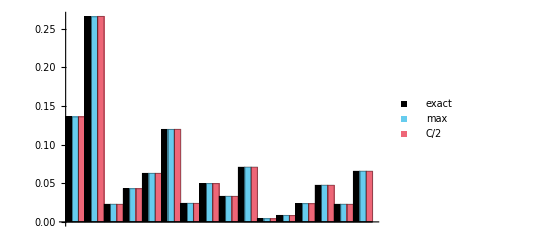

```mathematica
BarChart[T@{af9,mf9,cf9},ChartLayout->"Grouped",ChartStyle->{Black,blue,red},ChartLegends->Placed[PointLegend[{Black,blue,red},{"exact","max","C/2"},LegendMarkerSize->Auto,LegendMarkers->Style[■,40]],Bottom]]
```

```mathematica
expdf["comparefinalfreqs_1",%]
```

comparefinalfreqs_1.pdf

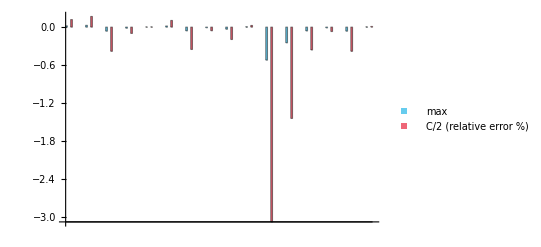

```mathematica
BarChart[T@{mf9-af9,cf9-af9}/af9*100,ChartLayout->"Grouped",ChartStyle->{blue,red},ChartLegends->Placed[PointLegend[{blue,red},{"max","C/2    (relative error %)"},LegendMarkerSize->Auto,LegendMarkers->Style[■,40]],Bottom]]
```

```mathematica
expdf["comparefinalfreqs_diff_1",%]
```

comparefinalfreqs_diff_1.pdf

```mathematica
wf9=(n*fr+1000/tx)/(n+1000);
wf6=(n*fs[list0[[1]]]+1000/tx)/(n+1000);
```

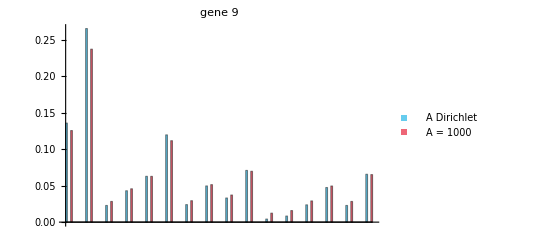
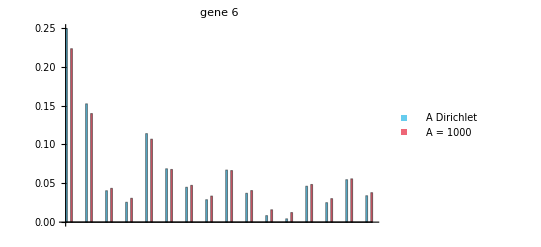

```mathematica
g96=Grid[{{BarChart[T@{af9,wf9},ChartLayout->"Grouped",ChartStyle->{blue,red},ChartLegends->Placed[PointLegend[{blue,red},{"A Dirichlet","A = 1000"},LegendMarkerSize->Auto,LegendMarkers->Style[■,40]],Bottom],PlotLabel->"gene 9"]},{BarChart[T@{af,wf6},ChartLayout->"Grouped",ChartStyle->{blue,red},ChartLegends->Placed[PointLegend[{blue,red},{"A Dirichlet","A = 1000"},LegendMarkerSize->Auto,LegendMarkers->Style[■,40]],Bottom],PlotLabel->"gene 6"]}}]
```

```mathematica
Export["gene9vs6.pdf",g96]
```

gene9vs6.pdf

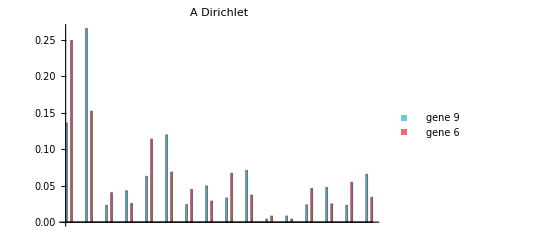
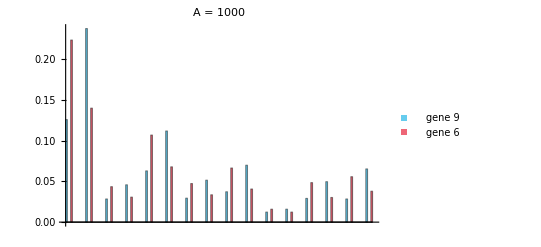

```mathematica
g96=Grid[{{BarChart[T@{af9,af},ChartLayout->"Grouped",ChartStyle->{blue,red},ChartLegends->Placed[PointLegend[{blue,red},{"gene 9","gene 6"},LegendMarkerSize->Auto,LegendMarkers->Style[■,40]],Bottom],PlotLabel->"A Dirichlet"]},{BarChart[T@{wf9,wf6},ChartLayout->"Grouped",ChartStyle->{blue,red},ChartLegends->Placed[PointLegend[{blue,red},{"gene 9","gene 6"},LegendMarkerSize->Auto,LegendMarkers->Style[■,40]],Bottom],PlotLabel->"A = 1000"]}}]
```

```mathematica
Export["gene9vs6_2.pdf",g96]
```

gene9vs6_2.pdf

```mathematica
Precision
```

```mathematica
gtab=Table[
maxt=maxi[k];
maxp=Exp@maxt[[1]];maxa=(ax/.maxt[[2]]);

Plot[ddir[ax,n,fs[k]]/maxp,{ax,Max[maxa-100,0],maxa+100},PlotRange->{0,1},Frame->Auto,Axes->None,FrameStyle->Directive[Black,Bold,18],
PlotLegends->Auto,FrameLabel->{{p[A | Length[k]],None},{A,None}}],{k,list0}];
```

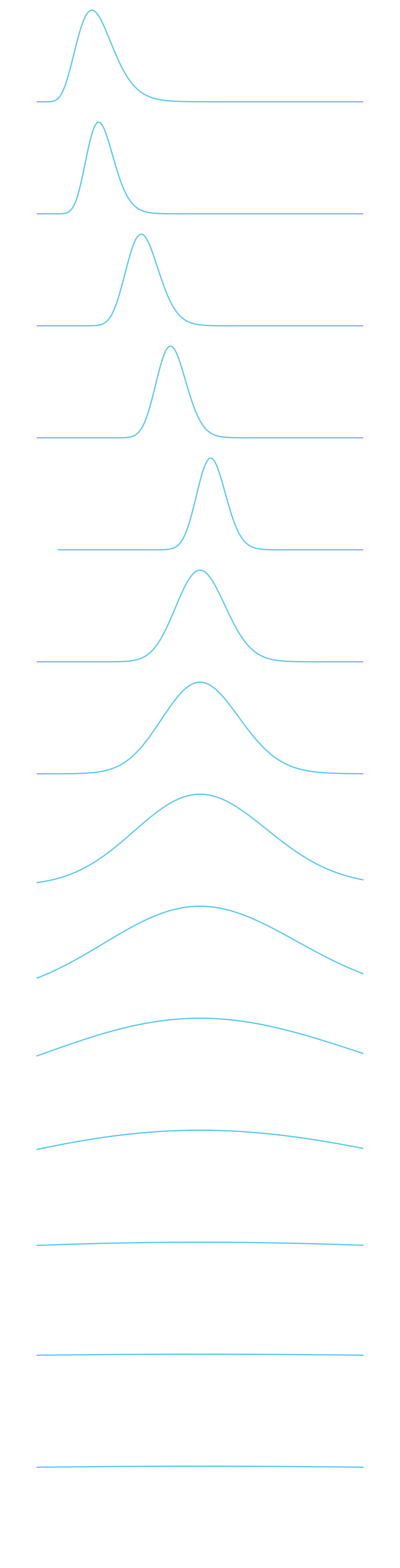
(-Graphics-)

```mathematica
gtab//MF
```